# Interactive Handwritten Character Classification:

## Alex O’Brien

## End Goal

```mathematica
DynamicModule[
{p={},g=Graphics[],i="Left-click to classify. Right-click to clear. Drag or touch to draw."},
EventHandler[Column[{
g=Dynamic[Graphics[
{
Black,Thickness[0.07],Line[p]
},
AspectRatio->1,
PlotRange->{{0,500},{0,500}},
ImageSize->500
]],
Dynamic[i]
}, Frame->All],
{
"MouseDown":> AppendTo[p,{}],
"MouseDragged":>AppendTo[p⟦Length[p]⟧,MousePosition["Graphics"]],
{"MouseClicked",2}:>Set[{p,i},{{},"Left-click to classify. Right-click to clear."}]
}]]
```

## A Rapid Introduction to Neural Networks

A graph where vertices represent mathematical operations of some kind and edges a flow of data, eventually mapping input to output.
The vertices are commonly referred to as neurons, and are arranged in layers of a single type.

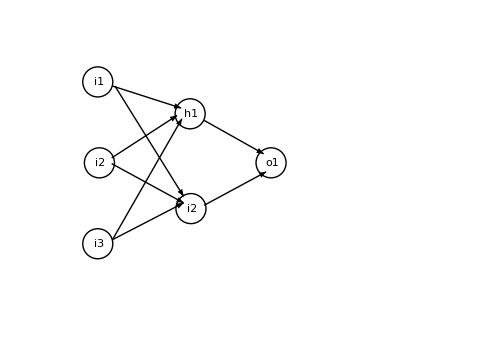

## A Rapid Introduction to Neural Networks

Each vertex, in the simplest case, has an activation function (e.g., Logistic Sigmoid):

```mathematica
Plot[LogisticSigmoid[x],{x,-8,8}]
```

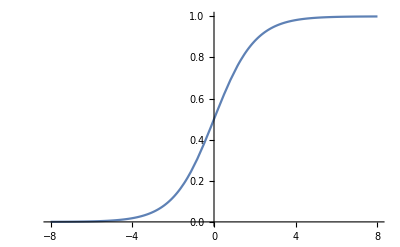

or Ramp:

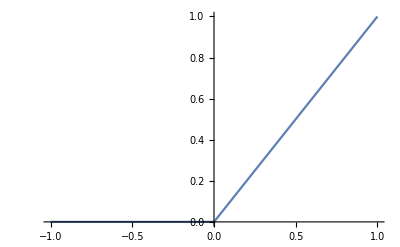

```mathematica
Plot[Ramp[x],{x,-1,1}]
```

Or even something like this:

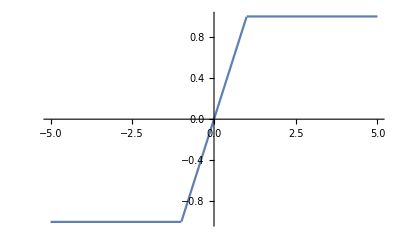

```mathematica
Plot[Clip[x],{x,-5,5}]
```

## A Rapid Introduction to Neural Networks

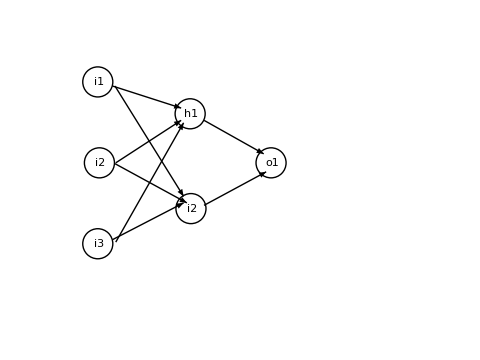

Data moving through the network is distorted by weights and biases, attached to neurons and edges.
Learning takes place by modifying weights and biases to minimize an error function.

## Training Data

Before we construct a network, we need data with which to teach it.
I used the NIST SD 19 handwritten digit database.
NetTrain expects data in the form of a list of associations between input and output.

```mathematica
charset=Join[ToUpperCase[Alphabet[]],Range[0,9]];
workDir=NotebookDirectory[];
importDirectory[d_]:=With[
{dir=workDir<>"data/org/"<>ToString[d]},
ParallelMap[File[#]->d&,FileNames["*.png",dir]]
]
```

```mathematica
dataFiles=RandomSample[importDirectory/@charset//Flatten];
trainingData=Partition[dataFiles,(Length[dataFiles]-1)/2-1]⟦1⟧;
validationData=Partition[dataFiles,(Length[dataFiles]-1)/2-1]⟦2⟧;
```

The data are split into validation and training sets.

## A Simple Network

A first attempt at a letter classifier.

Network design, even for experts is largely based on heuristics and not objective principles.
Let’s try something very simple:

```mathematica
simpleUntrained=NetInitialize[
NetChain[{
LinearLayer[108],
ElementwiseLayer[LogisticSigmoid],
LinearLayer[36],
ElementwiseLayer[LogisticSigmoid],
SoftmaxLayer[]
},
"Input"->NetEncoder[{"Image",{28,28},"ColorSpace"->"Grayscale"}],
"Output"->NetDecoder[{"Class",charset}]
]
]
```

```mathematica
simpleUntrained=Import[NotebookDirectory[]<>"simpleTrainedFinal.wlnet"];
```

LinearLayer just calculates w . x + b.
ElementWiseLayer applies the given function.
SoftmaxLayer normalizes a vector so its components sum to 1.
Training is easy:

```mathematica
NetTrain[simpleUntrained,trainingData,All,ValidationSet->validationData,TargetDevice->"GPU"]["TrainedNet"]
```

## Success?

```mathematica
simpleTrained=Import[NotebookDirectory[]<>"simpleTrainedFinal.wlnet"]
```

```mathematica
simpleTrained[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{O,4,2,3,B,N,O,9,3,8}

```mathematica
snEval["TopConfusions"]
```

{L→1,I→1,S→5,I→L,T→7,Z→2,B→6,M→N,S→3,Y→4}

That’s a no, then. On to more complicated things.

## Convolutional Neural Networks

Make use of convolutional layers, designed to emulate how real neurons respond to visual input.

Each neuron has a receptive field.

As well as pooling layers, which combine output from a cluster of neurons into one.

```mathematica
convUntrained=NetInitialize[
NetChain[{
ConvolutionLayer[20,4],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
ConvolutionLayer[40,9],
ElementwiseLayer[Ramp],
PoolingLayer[3,3],
LinearLayer[500],
ElementwiseLayer[Ramp],
LinearLayer[36],
SoftmaxLayer[]
},
"Input"->NetEncoder[{"Image",{28,28},"ColorSpace"->"Grayscale"}],
"Output"->NetDecoder[{"Class",charset}]
]]
```

```mathematica
convTrainingResult=NetTrain[convUntrained,trainingData,All,ValidationSet->validationData,TargetDevice->"GPU"]["TrainedNet"]
```

## CNN Evaluation

```mathematica
convTrained=Import[NotebookDirectory[]<>"convTrainedFinal.wlnet"]
```

```mathematica
convTrained[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{0,Y,2,3,B,H,O,9,S,P}

Looks promising...

0.876886

Hooray!

```mathematica
cvEval["TopConfusions"]
```

{L→1,O→0,I→1,Z→2,S→5,Q→9,G→9,I→L,B→6,C→E}

## Putting it Together

```mathematica
DynamicModule[
{p={},g=Graphics[],i="Left-click to classify. Right-click to clear.\nDrag or touch to draw."},
EventHandler[Column[{
g=Dynamic[Graphics[
{
Black,Thickness[0.07],Line[p]
},
AspectRatio->1,
PlotRange->{{0,500},{0,500}},
ImageSize->500
]],
Dynamic[i]
}, Frame->All],
{
"MouseDown":> AppendTo[p,{}],
"MouseDragged":>AppendTo[p⟦Length[p]⟧,MousePosition["Graphics"]],
{"MouseClicked",1}:>Set[i,convTrained[ImageResize[Rasterize[g],{28,28}]]],
{"MouseClicked",2}:>Set[{p,i},{{},"Left-click to classify. Right-click to clear."}]
}]]
```